# SI for Hierarchical Clustering

## Basics

```mathematica
home="/home/kamano/"
```

/home/kamano/

## Program

```mathematica
Needs["HierarchicalClustering`"]
```

```mathematica
<<(home<>"gitsrc/MATH_SCRIPT/SCRIPTS/List_operations.txt")
```

```mathematica
<<(home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Matrix_operations.txt")
```

```mathematica
<<(home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Chemicalform_operations.txt")
```

```mathematica
<<(home<>"gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt")
```

```mathematica
SetDirectory[home<>"TEXT/Chemical-form_search_by_Eigen/JSIK_Style"]
```

/home/kamano/TEXT/Chemical-form_search_by_Eigen/JSIK_Style

```mathematica
trReplace[mat_,li_]:=Module[{rls},
rls=Table[{n,n}->li[[n]],{n,Length[li]}];
ReplacePart[mat,rls]
]
```

```mathematica
elementAdjMat[mat_,vlist_]:=Module[{tr},
If[(Map[Head,vlist]//Flatten//Union)=={String},
tr=Map[ElementData[#,"AtomicNumber"]&,vlist],
tr=vlist
];
trReplace[mat,tr]
]
```

```mathematica
clSplitFlatten[cl_,n_]:=Map[ClusterFlatten,ClusterSplit[cl,n],{1}]/.ClusterFlatten->List
```

```mathematica
dAreaRatio[pt_]:=Module[{spt,plotArea,baseArea},
spt=Sort[pt];
plotArea=Area[Polygon[pt]];
baseArea=Area[Polygon[{spt[[1]],{0,1},{spt[[-1]][[1]],1},spt[[-1]]}]];
plotArea/baseArea
]
```

## Data

```mathematica
cc=ChemicalData["Classes"];
```

```mathematica
(*Save["figs",cc]*)
```

```mathematica
AA=ChemicalData["AminoAcids"]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
num = Length[AA]
```

20

```mathematica
(*Save["figs",AA]*)
```

```mathematica
AAName=Map[ChemicalData[#,"Name"]&,AA]
```

{glycine,L-alanine,L-serine,L-proline,L-valine,L-threonine,L-cysteine,L-isoleucine,L-leucine,L-asparagine,L-aspartic acid,L-glutamine,L-lysine,L-glutamic acid,L-methionine,L-histidine,L-phenylalanine,L-arginine,L-tyrosine,L-tryptophan}

```mathematica
(*Save["figs",AAName]*)
```

```mathematica
AAFig=Map[ChemicalData[#]&,AA];
```

```mathematica
AAFig45=Map[Graphics[#[[1]] , ImageSize->45]&, AAFig]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(AAAdjMat=Map[(ChemicalData[#,"AdjacencyMatrix"]//Normal)&,AA])//Short
```

{{{0,1,1,0,0,0,0,0,1,1},{1,0,0,1,2,0,0,0,0,0},«6»,{1,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0}},{«1»},«16»,{«1»},{«1»}}

```mathematica
(*Save["figs",AAAdjMat]*)
```

```mathematica
AAVT=Map[ChemicalData[#,"VertexTypes"]&,AA]
```

{{C,C,N,O,O,H,H,H,H,H},{O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,N,O,O,H,H,H,H,C,O,C,H,H,H,H,H},{S,O,O,N,C,C,C,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,O,O,H,H,H,H,H,H,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,H,H,H,H,H,H,H},{O,O,O,N,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{O,O,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{S,O,O,N,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{O,O,N,N,N,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H},{O,O,N,C,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,N,C,N,N,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,O,C,C,C,N,O,O,H,H,H,H,H,H,H,H,H,H,H},{C,C,C,C,C,C,N,C,C,C,H,C,H,H,H,H,H,H,H,N,C,H,H,H,O,O,H}}

```mathematica
(*Save["figs",AAVT]*)
```

```mathematica
(elmAAAdjMat=Table[elementAdjMat[AAAdjMat[[n]],AAVT[[n]]],{n,Length[AAAdjMat]}])//Length
```

20

```mathematica
(*Save["figs",elmAAAdjMat]*)
```

```mathematica
(AADmat=Outer[eigenSpectrumDistance,elmAAAdjMat,elmAAAdjMat,1])//Dimensions
```

{20,20}

```mathematica
(*Save["figs",AADmat]*)
```

```mathematica
bondlist=Table[ChemicalData[AA[[n]],"BondTally"],{n,num}]
```

{{{{{C,C},1},1},{{{C,H},1},2},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},2},{{{H,O},1},1}},{{{{C,C},1},2},{{{C,H},1},4},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},2},{{{H,O},1},1}},{{{{C,C},1},2},{{{C,H},1},3},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},2},{{{H,N},1},2},{{{H,O},1},2}},{{{{C,C},1},4},{{{C,H},1},7},{{{C,N},1},2},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},1},{{{H,O},1},1}},{{{{C,C},1},4},{{{C,H},1},8},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},2},{{{H,O},1},1}},{{{{C,C},1},3},{{{C,H},1},5},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},2},{{{H,N},1},2},{{{H,O},1},2}},{{{{C,C},1},2},{{{C,H},1},3},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},1},{{{C,S},1},1},{{{H,N},1},2},{{{H,O},1},1},{{{H,S},1},1}},{{{{C,C},1},5},{{{C,H},1},10},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},2},{{{H,O},1},1}},{{{{C,C},1},5},{{{C,H},1},10},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},2},{{{H,O},1},1}},{{{{C,C},1},3},{{{C,H},1},3},{{{C,N},1},2},{{{C,O},2},2},{{{C,O},1},1},{{{H,N},1},4},{{{H,O},1},1}},{{{{C,C},1},3},{{{C,H},1},3},{{{C,N},1},1},{{{C,O},2},2},{{{C,O},1},2},{{{H,N},1},2},{{{H,O},1},2}},{{{{C,C},1},4},{{{C,H},1},5},{{{C,N},1},2},{{{C,O},2},2},{{{C,O},1},1},{{{H,N},1},5}},{{{{C,C},1},5},{{{C,H},1},9},{{{C,N},1},2},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},4},{{{H,O},1},1}},{{{{C,C},1},4},{{{C,H},1},5},{{{C,N},1},1},{{{C,O},2},2},{{{C,O},1},2},{{{H,N},1},2},{{{H,O},1},2}},{{{{C,C},1},3},{{{C,H},1},8},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},1},{{{C,S},1},2},{{{H,N},1},2},{{{H,O},1},1}},{{{{C,C},2},1},{{{C,C},1},3},{{{C,H},1},5},{{{C,N},2},1},{{{C,N},1},4},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},3},{{{H,O},1},1}},{{{{C,C},2},3},{{{C,C},1},6},{{{C,H},1},8},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},2},{{{H,O},1},1}},{{{{C,C},1},4},{{{C,H},1},7},{{{C,N},2},1},{{{C,N},1},4},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},6},{{{H,O},1},1}},{{{{C,C},2},3},{{{C,C},1},6},{{{C,H},1},7},{{{C,N},1},1},{{{C,O},2},1},{{{C,O},1},2},{{{H,N},1},2},{{{H,O},1},2}},{{{{C,C},2},4},{{{C,C},1},7},{{{C,H},1},8},{{{C,N},1},3},{{{C,O},2},1},{{{C,O},1},1},{{{H,N},1},3},{{{H,O},1},1}}}

```mathematica
bondclass=Cases[bondlist,{_String,_String},{0,Infinity}]//Union
```

{{C,C},{C,H},{C,N},{C,O},{C,S},{H,N},{H,O},{H,S}}

```mathematica
bonding=Table[Total[Map[#[[2]]&,Cases[bondlist[[n]],{{bondclass[[m]],_Integer},_Integer},{0,Infinity}]]],{n,Length[bondlist]},{m,Length[bondclass]}]
```

{{1,2,1,2,0,2,1,0},{2,4,1,2,0,2,1,0},{2,3,1,3,0,2,2,0},{4,7,2,2,0,1,1,0},{4,8,1,2,0,2,1,0},{3,5,1,3,0,2,2,0},{2,3,1,2,1,2,1,1},{5,10,1,2,0,2,1,0},{5,10,1,2,0,2,1,0},{3,3,2,3,0,4,1,0},{3,3,1,4,0,2,2,0},{4,5,2,3,0,5,0,0},{5,9,2,2,0,4,1,0},{4,5,1,4,0,2,2,0},{3,8,1,2,2,2,1,0},{4,5,5,2,0,3,1,0},{9,8,1,2,0,2,1,0},{4,7,5,2,0,6,1,0},{9,7,1,3,0,2,2,0},{11,8,3,2,0,3,1,0}}

## Clustering(Eigen)

Hierarchical Cluster

```mathematica
ag["A"]=DirectAgglomerate[AADmat,Linkage->"Average"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[1,Cluster[Cluster[Cluster[2,7,0.292172,1,1],3,0.669325,2,1],6,0.798298,3,1],1.31674,1,4],Cluster[Cluster[Cluster[12,Cluster[Cluster[14,10,0.468095,1,1],11,0.5617,2,1],0.704903,1,3],Cluster[16,18,0.92273,1,1],1.56884,4,2],Cluster[Cluster[4,Cluster[Cluster[5,15,0.466146,1,1],Cluster[8,9,0.522399,1,1],0.835355,2,2],0.928711,1,4],13,1.04394,5,1],1.81684,6,6],2.22909,5,12],Cluster[20,Cluster[19,17,0.588454,1,1],1.63161,1,2],4.08975,17,3]

```mathematica
ag["WA"]=DirectAgglomerate[AADmat,Linkage->"WeightedAverage"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],3,0.669325,2,1],0.994135,1,3],Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.844398,2,1],0.927675,1,3],Cluster[Cluster[5,15,0.466146,1,1],6,0.819333,2,1],1.08802,4,3],1.58344,4,7],Cluster[Cluster[18,16,0.92273,1,1],Cluster[Cluster[11,Cluster[14,10,0.468095,1,1],0.5617,1,2],12,0.659033,3,1],1.65253,2,4],2.03674,11,6],Cluster[Cluster[17,19,0.588454,1,1],20,1.63161,2,1],3.73837,17,3]

```mathematica
ag["W"]=DirectAgglomerate[AADmat,Linkage->"Ward"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[Cluster[Cluster[1,Cluster[Cluster[2,7,0.292172,1,1],Cluster[3,6,0.71254,1,1],1.05103,2,2],1.43447,1,4],Cluster[Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.951732,2,1],1.02298,1,3],Cluster[5,15,0.466146,1,1],1.43198,4,2],4.67907,5,6],Cluster[Cluster[16,18,0.92273,1,1],Cluster[12,Cluster[Cluster[14,10,0.468095,1,1],11,0.592902,2,1],0.723301,1,3],3.19682,2,4],7.56004,11,6],Cluster[Cluster[17,19,0.588454,1,1],20,1.97933,2,1],12.9788,17,3]

```mathematica
ag["C"]=DirectAgglomerate[AADmat,Linkage->"Centroid"]
```

DirectAgglomerate::ties: 1 ties have been detected; reordering input may produce a different result.

Cluster[Cluster[1,Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[2,7,0.292172,1,1],3,0.596282,2,1],6,0.645681,3,1],Cluster[5,15,0.466146,1,1],0.646992,4,2],Cluster[4,Cluster[Cluster[8,9,0.522399,1,1],13,0.713799,2,1],0.681986,1,3],0.729913,6,4],Cluster[12,Cluster[Cluster[14,10,0.468095,1,1],11,0.444676,2,1],0.482201,1,3],1.02204,10,4],Cluster[16,18,0.92273,1,1],1.27935,14,2],1.46387,1,16],Cluster[20,Cluster[19,17,0.588454,1,1],1.4845,1,2],2.54486,17,3]

Hierarchical validation

```mathematica
Map[Length,(agsp["A"]=Table[ClusterSplit[ag["A"],n],{n,20}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL["A"]=Map[ClusterFlatten,agsp["A"],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps["A"]=Table[piDMG[AADmat,agspFL["A"][[n]]],{n,20}]
```

{20.,7.11861,7.20962,7.42148,7.63739,7.99359,8.70209,9.5186,10.3446,11.162,11.9413,12.776,13.6574,14.5075,15.4058,16.2942,17.2057,18.1269,19.0488,20.}

```mathematica
Map[Length,(agsp["W"]=Table[ClusterSplit[ag["W"],n],{n,20}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL["W"]=Map[ClusterFlatten,agsp["W"],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps["W"]=Table[piDMG[AADmat,agspFL["W"][[n]]],{n,20}]
```

{20.,7.11861,7.18004,7.42148,7.57266,7.99359,8.70209,9.51355,10.2962,11.1119,11.9181,12.7504,13.6322,14.5075,15.3948,16.2942,17.2057,18.1269,19.0488,20.}

```mathematica
Map[Length,(agsp["WA"]=Table[ClusterSplit[ag["WA"],n],{n,20}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL["WA"]=Map[ClusterFlatten,agsp["WA"],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps["WA"]=Table[piDMG[AADmat,agspFL["WA"][[n]]],{n,20}]
```

{20.,7.11861,7.18004,6.96998,7.26336,7.97071,8.7945,9.53531,10.3385,11.1561,11.9611,12.776,13.6236,14.5075,15.4058,16.2942,17.2057,18.1269,19.0488,20.}

```mathematica
Map[Length,(agsp["C"]=Table[ClusterSplit[ag["C"],n],{n,20}])]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
agspFL["C"]=Map[ClusterFlatten,agsp["C"],{2}]/.ClusterFlatten->List;
```

```mathematica
cvisteps["C"]=Table[piDMG[AADmat,agspFL["C"][[n]]],{n,20}]
```

{20.,7.11861,6.21464,6.6581,7.27153,7.94482,8.71099,9.55628,10.3587,11.1548,11.9413,12.776,13.6236,14.5204,15.43,16.3164,17.2373,18.1272,19.0488,20.}

Dendrogram

Validation of agglomerated distance (sorted)

Agglomerated distance

```mathematica
ad["A"]=Append[Sort[Map[#[[3]]&,Cases[ag["A"],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{4.08975,2.22909,1.81684,1.63161,1.56884,1.31674,1.04394,0.928711,0.92273,0.835355,0.798298,0.704903,0.669325,0.588454,0.5617,0.522399,0.468095,0.466146,0.292172,0}

```mathematica
ad["WA"]=Append[Sort[Map[#[[3]]&,Cases[ag["WA"],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{3.73837,2.03674,1.65253,1.63161,1.58344,1.08802,0.994135,0.927675,0.92273,0.844398,0.819333,0.669325,0.659033,0.588454,0.5617,0.522399,0.468095,0.466146,0.292172,0}

```mathematica
ad["W"]=Append[Sort[Map[#[[3]]&,Cases[ag["W"],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{12.9788,7.56004,4.67907,3.19682,1.97933,1.43447,1.43198,1.05103,1.02298,0.951732,0.92273,0.723301,0.71254,0.592902,0.588454,0.522399,0.468095,0.466146,0.292172,0}

```mathematica
ad["C"]=Append[Sort[Map[#[[3]]&,Cases[ag["C"],Cluster[_,_,_,_,_],{0,Infinity}]],#1>#2&],0]
```

{2.54486,1.4845,1.46387,1.27935,1.02204,0.92273,0.729913,0.713799,0.681986,0.646992,0.645681,0.596282,0.588454,0.522399,0.482201,0.468095,0.466146,0.444676,0.292172,0}

Num of members depending on distance

```mathematica
cls["A"]=Append[Table[Cases[ag["A"],Cluster[_,_,x_,_,_]/;x≤ad["A"][[1]]&&x≥ad["A"][[n]],{0,Infinity}]//Length,{n,num-1}],num]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
cls["WA"]=Append[Table[Cases[ag["WA"],Cluster[_,_,x_,_,_]/;x≤ad["WA"][[1]]&&x≥ad["WA"][[n]],{0,Infinity}]//Length,{n,num-1}],num]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
cls["W"]=Append[Table[Cases[ag["W"],Cluster[_,_,x_,_,_]/;x≤ad["W"][[1]]&&x≥ad["W"][[n]],{0,Infinity}]//Length,{n,num-1}],num]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
cls["C"]=Append[Table[Cases[ag["C"],Cluster[_,_,x_,_,_]/;x≤ad["C"][[1]]&&x≥ad["C"][[n]],{0,Infinity}]//Length,{n,num-1}],num]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Validation-plot points

```mathematica
pt["A"]=Transpose[{ad["A"],cvisteps["A"]}]
```

{{4.08975,20.},{2.22909,7.11861},{1.81684,7.20962},{1.63161,7.42148},{1.56884,7.63739},{1.31674,7.99359},{1.04394,8.70209},{0.928711,9.5186},{0.92273,10.3446},{0.835355,11.162},{0.798298,11.9413},{0.704903,12.776},{0.669325,13.6574},{0.588454,14.5075},{0.5617,15.4058},{0.522399,16.2942},{0.468095,17.2057},{0.466146,18.1269},{0.292172,19.0488},{0,20.}}

```mathematica
pt["WA"]=Transpose[{ad["WA"],cvisteps["WA"]}]
```

{{3.73837,20.},{2.03674,7.11861},{1.65253,7.18004},{1.63161,6.96998},{1.58344,7.26336},{1.08802,7.97071},{0.994135,8.7945},{0.927675,9.53531},{0.92273,10.3385},{0.844398,11.1561},{0.819333,11.9611},{0.669325,12.776},{0.659033,13.6236},{0.588454,14.5075},{0.5617,15.4058},{0.522399,16.2942},{0.468095,17.2057},{0.466146,18.1269},{0.292172,19.0488},{0,20.}}

```mathematica
pt["W"]=Transpose[{ad["W"],cvisteps["W"]}]
```

{{12.9788,20.},{7.56004,7.11861},{4.67907,7.18004},{3.19682,7.42148},{1.97933,7.57266},{1.43447,7.99359},{1.43198,8.70209},{1.05103,9.51355},{1.02298,10.2962},{0.951732,11.1119},{0.92273,11.9181},{0.723301,12.7504},{0.71254,13.6322},{0.592902,14.5075},{0.588454,15.3948},{0.522399,16.2942},{0.468095,17.2057},{0.466146,18.1269},{0.292172,19.0488},{0,20.}}

```mathematica
pt["C"]=Transpose[{ad["C"],cvisteps["C"]}]
```

{{2.54486,20.},{1.4845,7.11861},{1.46387,6.21464},{1.27935,6.6581},{1.02204,7.27153},{0.92273,7.94482},{0.729913,8.71099},{0.713799,9.55628},{0.681986,10.3587},{0.646992,11.1548},{0.645681,11.9413},{0.596282,12.776},{0.588454,13.6236},{0.522399,14.5204},{0.482201,15.43},{0.468095,16.3164},{0.466146,17.2373},{0.444676,18.1272},{0.292172,19.0488},{0,20.}}

Cumulative validation

```mathematica
area["C"]=Area[Polygon[Sort[pt["C"]]]]
```

18.7645

```mathematica
base["C"]=Area[Polygon[{Sort[pt["C"]][[1]],{0,1},{Sort[pt["C"]][[-1]][[1]],1},Sort[pt["C"]][[-1]]}]]
```

48.3524

```mathematica
dAreaRatio[pt["A"]]
```

0.403983

```mathematica
dAreaRatio[pt["WA"]]
```

0.397261

```mathematica
dAreaRatio[pt["W"]]
```

0.491365

```mathematica
dAreaRatio[pt["C"]]
```

0.388078

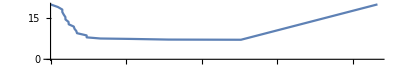

```mathematica
ListPlot[pt["W"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

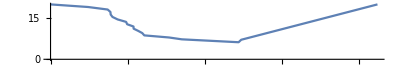

```mathematica
ListPlot[pt["C"],Joined->True,PlotRange->All,AspectRatio->1/6]
```

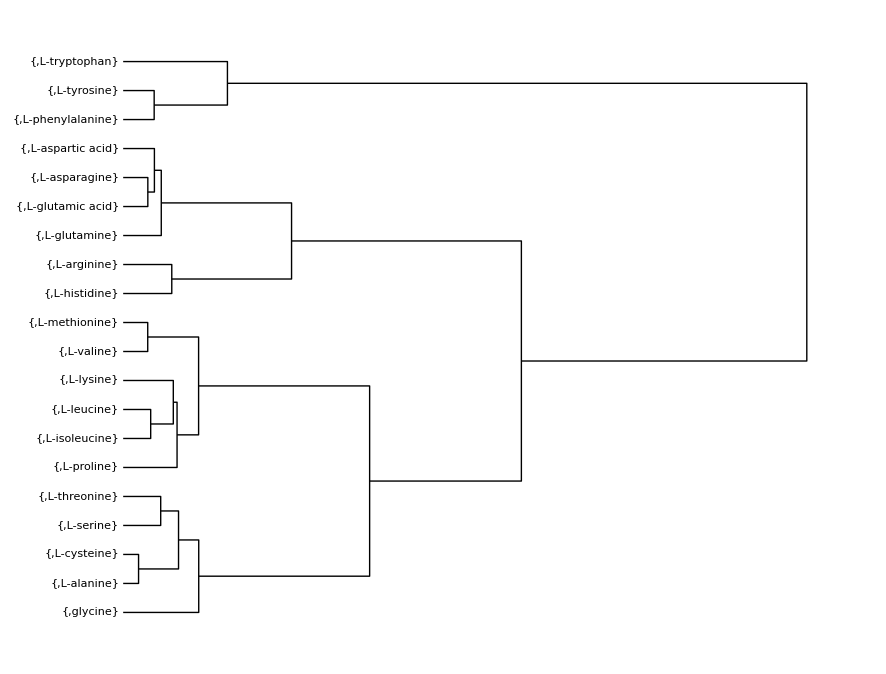

```mathematica
DendrogramPlot[ag["W"],LeafLabels->({AAFig45[[#]],AAName[[#]]}&),Orientation->Right,AspectRatio->0.76]
```